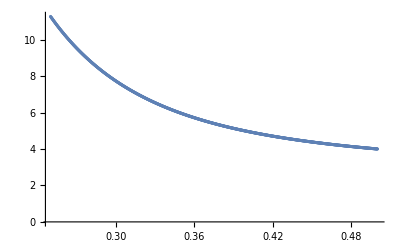

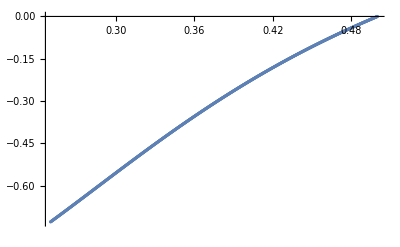

```mathematica
(*史瓦西时空，z坐标径向流方程演化到zc*)
Clear["Global`*"]
r0=2.0;
ω=0.2;l=0;
evz[σ_,z_]:={If[z==r0^-1,(4 ω^2 r0^4-l(l+1)*r0^2)/(-I*ω-2 ω^2 r0),(-ω^2 z^-2/(1-r0*z)+l(l+1))/(I*ω*z^2)-(I*ω)/(1-r0*z)σ^2],1}
z=r0^-1;σ=r0^2;
st=-0.00025;times=1000;
snaps={};
Monitor[Label["ev"];Ψ={σ,z};
R1=Apply[evz,Ψ];R2=Apply[evz,Ψ+st/2 R1];
R3=Apply[evz,Ψ+st/2 R2];R4=Apply[evz,Ψ+st*R3];
{σ,z}+=st/6(R1+2R2+2R3+R4);times=times-1;AppendTo[snaps,Ψ];If[times>0,Goto["ev"]],times]
ListPlot[Table[{snaps[[i,2]],Abs@snaps[[i,1]]},{i,1,Length[snaps]}],PlotRange->All]
ListPlot[Table[{snaps[[i,2]],Arg@snaps[[i,1]]},{i,1,Length[snaps]}],PlotRange->All]
```

0.25

3.01277+3.36668 ⅈ

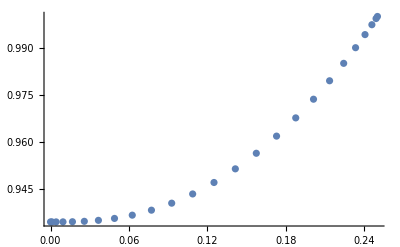

```mathematica
(*z==zc处边界条件∂_z R==σ*R*)
zc=z
σ*=(I*ω)/(1-r0*z)
Clear[z]
n=25;
f[z_]:=1-r0*z
x=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
c=Table[1.0,{i,1,n}];c[[1]]=2.0;c[[n]]=2.0;
d=2/zc Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];
d-=DiagonalMatrix[Total[d,{2}]];
z=(1+x)/2 zc;
fz=f[z];
lop=d.DiagonalMatrix[z^2 fz].d+2I*ω(1-r0^2 z^2)(-d)+DiagonalMatrix[2I*ω*r0^2 z-r0*z+(ω^2 r0^2)/fz(2-r0^2 z^2)-l(l+1)];
lop[[1]]=IdentityMatrix[n][[1]];
up=LinearSolve[lop,{1.0}~Join~Table[0.0,{n-1}]];
ListPlot[Transpose[{z,Abs@up}],PlotRange->All]
```

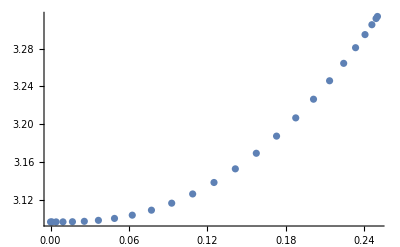

0.301765

0.518084

```mathematica
bdry=(-(-zc^2 d[[1]].up+I*ω*up[[1]])-zc*(-1+I*ω*r0)up[[1]]-zc^2 σ*up[[1]])Exp[I*ω(1/zc+r0*Log[1/(r0*zc)])];
lop=d.DiagonalMatrix[z^2 fz].d-2I*ω(1-r0^2 z^2)(-d)+DiagonalMatrix[-2I*ω*r0^2 z-r0*z+(ω^2 r0^2)/fz(2-r0^2 z^2)-l(l+1)];
lop[[1]]=(-(-zc^2 d[[1]]-I*ω*IdentityMatrix[n][[1]])-zc*(-1-I*ω*r0)IdentityMatrix[n][[1]]-zc^2 σ*IdentityMatrix[n][[1]])Exp[-I*ω(1/zc+r0*Log[1/(r0*zc)])];
um=LinearSolve[lop,{bdry}~Join~Table[0.0,{n-1}]];
ListPlot[Transpose[{z,Abs@um}],PlotRange->All]
Abs[up[[-1]]/um[[-1]]]
Arg[up[[-1]]/um[[-1]]]
```

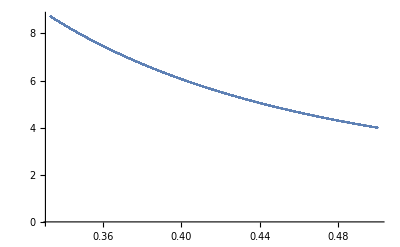

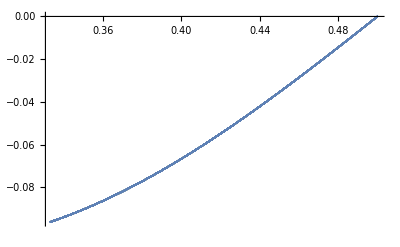

```mathematica
(*同上，改用等r步进以适应较大ω需演化到较大r，但大ω情形st需减小，显示结果对近视界处流方程误差较敏感*)
Clear["Global`*"]
r0=2.0;
ω=1.2;l=1;(*若l=0行为更差*)
evz[σ_,z_]:={If[z==r0^-1,(4 ω^2 r0^4-l(l+1)*r0^2)/(-I*ω-2 ω^2 r0),(-ω^2 z^-2/(1-r0*z)+l(l+1))/(I*ω*z^2)-(I*ω)/(1-r0*z)σ^2],1}
z=r0^-1;σ=r0^2;
stb=0.00002;times=50000;
snaps={};
Monitor[Label["ev"];Ψ={σ,z};st=-z^2 stb;
R1=Apply[evz,Ψ];R2=Apply[evz,Ψ+st/2 R1];
R3=Apply[evz,Ψ+st/2 R2];R4=Apply[evz,Ψ+st*R3];
{σ,z}+=st/6(R1+2R2+2R3+R4);times=times-1;AppendTo[snaps,Ψ];If[times>0,Goto["ev"]],times]
ListPlot[Table[{snaps[[i,2]],Abs@snaps[[i,1]]},{i,1,Length[snaps]}],PlotRange->All]
ListPlot[Table[{snaps[[i,2]],Arg@snaps[[i,1]]},{i,1,Length[snaps]}],PlotRange->All]
```

0.333332

3.01697+31.2524 ⅈ

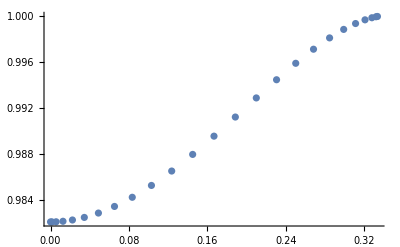

```mathematica
(*z==zc处边界条件∂_z R==σ*R，改变zc和模式数n结果已基本收敛，但继续增大n会导致LinearSolve警告矩阵条件差*)
zc=z
σ*=(I*ω)/(1-r0*z)
Clear[z]
n=25;
f[z_]:=1-r0*z
x=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
c=Table[1.0,{i,1,n}];c[[1]]=2.0;c[[n]]=2.0;
d=2/zc Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];
d-=DiagonalMatrix[Total[d,{2}]];
z=(1+x)/2 zc;
fz=f[z];
lop=d.DiagonalMatrix[z^2 fz].d+2I*ω(1-r0^2 z^2)(-d)+DiagonalMatrix[2I*ω*r0^2 z-r0*z+(ω^2 r0^2)/fz(2-r0^2 z^2)-l(l+1)];
lop[[1]]=IdentityMatrix[n][[1]];
up=LinearSolve[lop,{1.0}~Join~Table[0.0,{n-1}]];
ListPlot[Transpose[{z,Abs@up}],PlotRange->All]
```

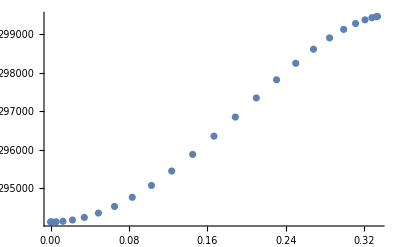

3.33928×10^-6

-0.110111

```mathematica
bdry=(-(-zc^2 d[[1]].up+I*ω*up[[1]])-zc*(-1+I*ω*r0)up[[1]]-zc^2 σ*up[[1]])Exp[I*ω(1/zc+r0*Log[1/(r0*zc)])];
lop=d.DiagonalMatrix[z^2 fz].d-2I*ω(1-r0^2 z^2)(-d)+DiagonalMatrix[-2I*ω*r0^2 z-r0*z+(ω^2 r0^2)/fz(2-r0^2 z^2)-l(l+1)];
lop[[1]]=(-(-zc^2 d[[1]]-I*ω*IdentityMatrix[n][[1]])-zc*(-1-I*ω*r0)IdentityMatrix[n][[1]]-zc^2 σ*IdentityMatrix[n][[1]])Exp[-I*ω(1/zc+r0*Log[1/(r0*zc)])];
um=LinearSolve[lop,{bdry}~Join~Table[0.0,{n-1}]];
ListPlot[Transpose[{z,Abs@um}],PlotRange->All]
Abs[up[[-1]]/um[[-1]]]
Arg[up[[-1]]/um[[-1]]]
```

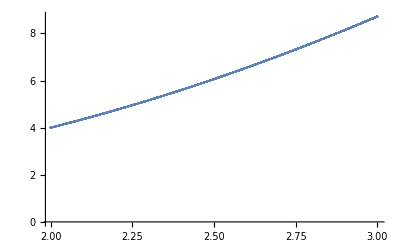

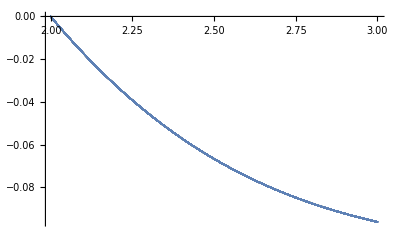

```mathematica
(*同上，改用r演化进行比较，同样显示结果对近视界处流方程误差较敏感*)
Clear["Global`*"]
r0=2.0;
ω=1.2;l=1;(*若l=0行为更差*)
evz[σ_,r_]:={If[r==r0,(4 ω^2 r0^2-l(l+1))/(I*ω+2 ω^2 r0),-(-ω^2 r^2/(1-r0/r)+l(l+1))/(I*ω)+(I*ω)/(r^2-r0*r)σ^2],1}
r=r0;σ=r0^2;
st=0.00002;times=50000;
snaps={};
Monitor[Label["ev"];Ψ={σ,r};
R1=Apply[evz,Ψ];R2=Apply[evz,Ψ+st/2 R1];
R3=Apply[evz,Ψ+st/2 R2];R4=Apply[evz,Ψ+st*R3];
{σ,r}+=st/6(R1+2R2+2R3+R4);times=times-1;AppendTo[snaps,Ψ];If[times>0,Goto["ev"]],times]
ListPlot[Table[{snaps[[i,2]],Abs@snaps[[i,1]]},{i,1,Length[snaps]}],PlotRange->All]
ListPlot[Table[{snaps[[i,2]],Arg@snaps[[i,1]]},{i,1,Length[snaps]}],PlotRange->All]
```

0.333333

3.01696+31.2524 ⅈ

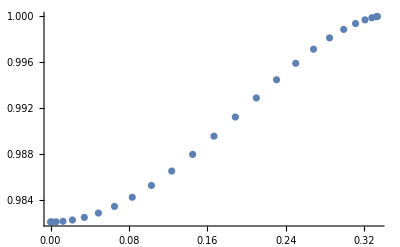

```mathematica
(*z==zc处边界条件∂_z R==σ*R，改变zc和模式数n结果已基本收敛，但继续增大n会导致LinearSolve警告矩阵条件差*)
zc=1/r
σ*=(I*ω)/(1-r0*zc)
n=25;
f[z_]:=1-r0*z
x=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
c=Table[1.0,{i,1,n}];c[[1]]=2.0;c[[n]]=2.0;
d=2/zc Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];
d-=DiagonalMatrix[Total[d,{2}]];
z=(1+x)/2 zc;
fz=f[z];
lop=d.DiagonalMatrix[z^2 fz].d+2I*ω(1-r0^2 z^2)(-d)+DiagonalMatrix[2I*ω*r0^2 z-r0*z+(ω^2 r0^2)/fz(2-r0^2 z^2)-l(l+1)];
lop[[1]]=IdentityMatrix[n][[1]];
up=LinearSolve[lop,{1.0}~Join~Table[0.0,{n-1}]];
ListPlot[Transpose[{z,Abs@up}],PlotRange->All]
```

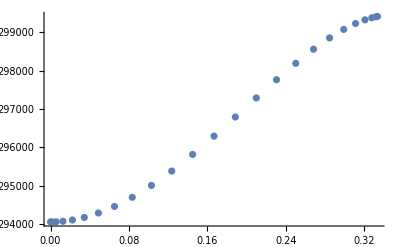

3.33991×10^-6

-0.110587

```mathematica
bdry=(-(-zc^2 d[[1]].up+I*ω*up[[1]])-zc*(-1+I*ω*r0)up[[1]]-zc^2 σ*up[[1]])Exp[I*ω(1/zc+r0*Log[1/(r0*zc)])];
lop=d.DiagonalMatrix[z^2 fz].d-2I*ω(1-r0^2 z^2)(-d)+DiagonalMatrix[-2I*ω*r0^2 z-r0*z+(ω^2 r0^2)/fz(2-r0^2 z^2)-l(l+1)];
lop[[1]]=(-(-zc^2 d[[1]]-I*ω*IdentityMatrix[n][[1]])-zc*(-1-I*ω*r0)IdentityMatrix[n][[1]]-zc^2 σ*IdentityMatrix[n][[1]])Exp[-I*ω(1/zc+r0*Log[1/(r0*zc)])];
um=LinearSolve[lop,{bdry}~Join~Table[0.0,{n-1}]];
ListPlot[Transpose[{z,Abs@um}],PlotRange->All]
Abs[up[[-1]]/um[[-1]]]
Arg[up[[-1]]/um[[-1]]]
```